```mathematica
n=10;
a=1;
b=0.5;
c=10;
d=10;
```

```mathematica
n=10
```

10

```mathematica
(*s=Array[(c-d)/n&,n]*)
s=Array[0&,n];
diag=Array[-(2a+b)-s[[#]]&,n];
diag[[1]]=-(a+b)-s[[1]];
diag[[n]]=-a-d-s[[n]];
A1=SparseArray[{
Band[{2,1}]->(a+b),
Band[{1,1}]->diag,
Band[{1,2}]->a
},{n,n}];
A1=Normal[A1];
A2=SparseArray[{
Band[{2,1}]->(a+b),
Band[{1,1}]->-diag,
Band[{1,2}]->a
},{n,n}];
A2=Normal[A2];
MatrixForm[A1]
MatrixForm[A2]
```

(-1.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.5 | -2.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.5 | -2.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.5 | -2.5 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | -2.5 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.5 | -2.5 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.5 | -2.5 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.5 | -2.5 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | -2.5 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | -11)

(1.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.5 | 2.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.5 | 2.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.5 | 2.5 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.5 | 2.5 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.5 | 2.5 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.5 | 2.5 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.5 | 2.5 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | 2.5 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | 11)

```mathematica
v1=Array[0&,n];
v1[[1]]=c;
v2=Array[0&,n];
v2[[1]]=c;
```

```mathematica
ClearAll[Y,expectation,expsystem,expinit]
```

```mathematica
Ys[t_]:=Table[Y[i][t],{i,1,n}]
```

```mathematica
expsystem=D[Ys[t],t]==A1.Ys[t]+v1;
Y0=Array[0&,n];
(*Y0[[1]]=1000;*)
(*Y0[[n]]=0;*)
expinit=Ys[0]==Y0;
```

```mathematica
(*sol=DSolve[{system,init},Ys[t],t];*)
```

```mathematica
expectation=NDSolveValue[{expsystem,expinit},Ys[t],{t,0,500}];
expectationfunc[t0_]:=expectation/.t->t0
```

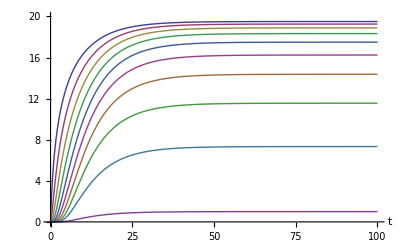

```mathematica
p=Plot[Evaluate[expectationfunc[t]],{t,0,100},AxesLabel->{t,Automatic},PlotRange->{0,20}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mrussell/phd/agent_based/gillespie

```mathematica
Export["exp.pdf",p]
```

exp.pdf

```mathematica
expdata=Table[Join[{t},expectationfunc[t]],{t,0,50,0.05}];
```

```mathematica
Export["exp.dat",expdata,"Table","FieldSeparators"->" "]
```

exp.dat

```mathematica
ClearAll[Z,variance,varsystem,varinit]
```

```mathematica
Zs[t_]:=Table[Z[i][t],{i,1,n}]
```

```mathematica
varsystem=D[Zs[t],t]==A2.expectationfunc[t]+v2+2 DiagonalMatrix[diag].Zs[t];
Z0=Array[0&,n];
(*Y0[[1]]=1000;*)
(*Y0[[n]]=0;*)
varinit=Zs[0]==Z0;
```

```mathematica
(*sol=DSolve[{system,init},Ys[t],t];*)
```

```mathematica
variance=NDSolveValue[{varsystem,varinit},Zs[t],{t,0,500}];
variancefunc[t0_]:=variance/.t->t0
```

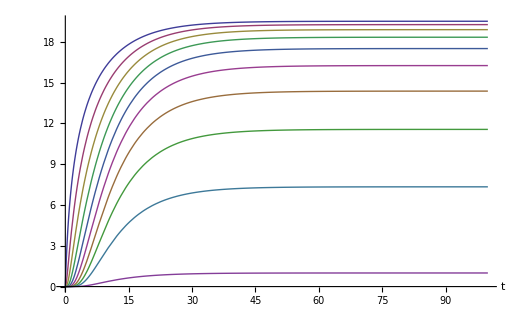

```mathematica
p=Plot[Evaluate[variancefunc[t]],{t,0,100},AxesLabel->{t,Automatic},PlotRange->Full]
```

```mathematica
vardata=Table[Join[{t},variancefunc[t]],{t,0,40,0.05}];
```

```mathematica
Export["var.dat",vardata,"Table","FieldSeparators"->" "]
```

var.dat